```mathematica
SetDirectory[NotebookDirectory[]];
data4=Import["my-big-mac-file.xlsx"][[1]][[2;;,{4,5}]];
info4[x_]:=(new=Array[f,33];c=1;
For[i=33*(x-1)+1,i≤33*x,i++,
new[[c]]=data4[[i]];c=c+1;
];
Return[new];)
```

```mathematica
datas=info4[1][[1;;,2]];
pp=Array[f,Length[datas]];
tsmod=TimeSeriesModelFit[datas,"ARMA"];
For[i=1,i≤33,i++,
pp[[i]]=TimeSeriesForecast[tsmod,1];
datas=AppendTo[datas,pp[[i]]];
tsmod=TimeSeriesModelFit[datas,"ARMA"];
]
```

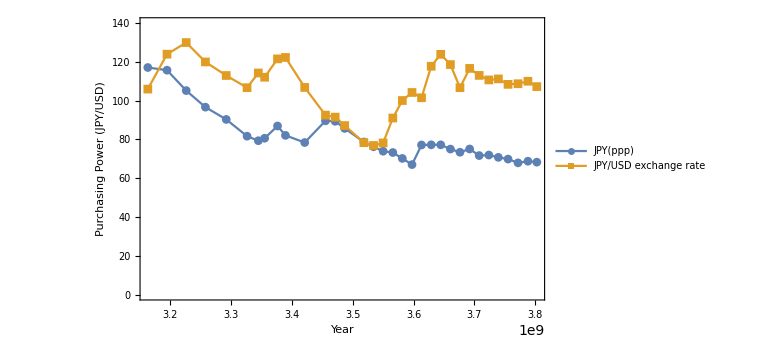

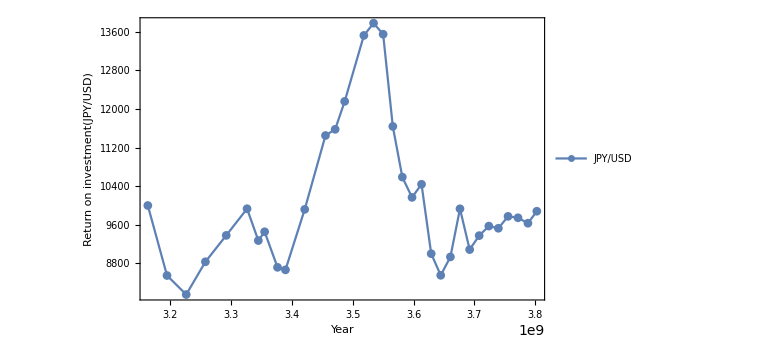

```mathematica
plot1=DateListPlot[{info4[6],info3[6]},PlotStyle->Thick,Frame->True,
FrameStyle->Directive[Black,20],PlotMarkers->Automatic,ImageSize->Large,FrameLabel->{"Year","Purchasing Power (JPY/USD)"},PlotLegends->{"JPY(ppp)","JPY/USD exchange rate"},PlotRange->{0,140}]

plot2=DateListPlot[{info2[6]},PlotStyle->Thick,Frame->True,FrameStyle->Directive[Black,20],PlotMarkers->Automatic,ImageSize->Large,FrameLabel->{"Year","Return on investment(JPY/USD)"},PlotLegends->{"JPY/USD"}]
```

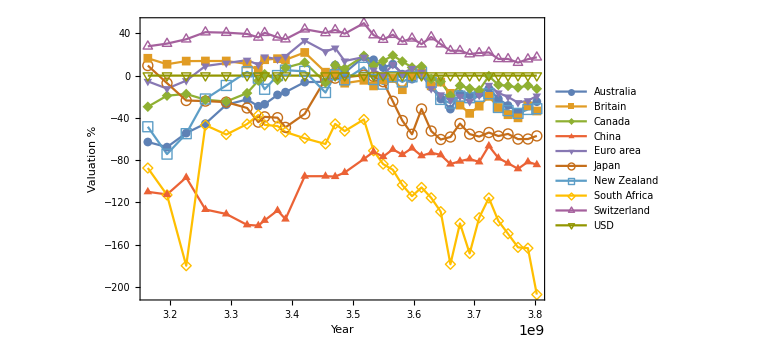

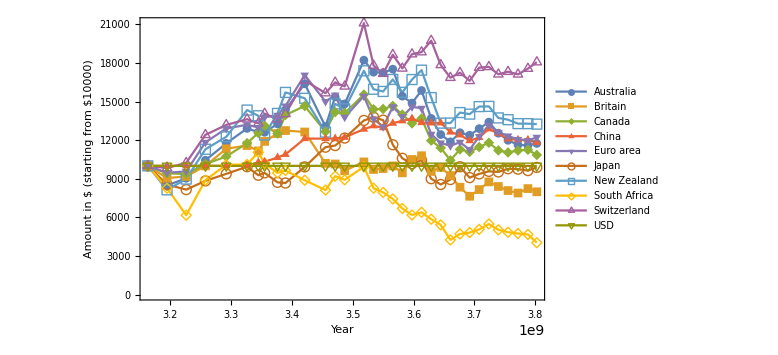

```mathematica
(*data:date vs value of valuation%
info= function that returns valuation vs time for a currency

data2=date vs investment value
info2=function that returns investment value vs time when money invested in currencies at 2000.

data3=date vs exchange price 
info3=function that returns exchange vs time for currencies
*)


(*Import data from excel file - date vs valuation *)
SetDirectory[NotebookDirectory[]];
data=Import["my-big-mac-file.xlsx"][[1]][[2;;,{4,7}]];
info[x_]:=(new=Array[f,33];c=1;
For[i=33*(x-1)+1,i≤33*x,i++,
new[[c]]=data[[i]];c=c+1;
];
Return[new];)

(*Import data from excel file - date vs investment value *)
data2=Import["my-big-mac-file.xlsx"][[1]][[2;;,{4,8}]];
info2[x_]:=(new=Array[f,33];c=1;
For[i=33*(x-1)+1,i≤33*x,i++,
new[[c]]=data2[[i]];c=c+1;
];
Return[new];)

(*Import data from excel file - date vs exchange price *)
data3=Import["my-big-mac-file.xlsx"][[1]][[2;;,{4,3}]];
info3[x_]:=(new=Array[f,33];c=1;
For[i=33*(x-1)+1,i≤33*x,i++,
new[[c]]=data3[[i]];c=c+1;
];
Return[new];)


plot1=DateListPlot[{info[1],info[2],info[3],info[4],info[5],info[6],info[7],info[8],info[9],info[10]},PlotStyle->Thick,Frame->True,FrameStyle->Directive[Black,20],PlotMarkers->Automatic,ImageSize->Large,FrameLabel->{"Year","Valuation %"},PlotLegends->{"Australia","Britain","Canada","China","Euro area","Japan","New Zealand","South Africa","Switzerland","USD"}]


plot2=DateListPlot[{info2[1],info2[2],info2[3],info2[4],info2[5],info2[6],info2[7],info2[8],info2[9],info2[10]},PlotStyle->Thick,Frame->True,FrameStyle->Directive[Black,20],PlotMarkers->Automatic,ImageSize->Large,FrameLabel->{"Year","Amount in $ (starting from $10000)"},PlotLegends->{"Australia","Britain","Canada","China","Euro area","Japan","New Zealand","South Africa","Switzerland","USD"}]



Export["valuation over 20 years.png",plot1]

Export["$10000 invested in 2000.png",plot2]
```

```mathematica
(*function to extract specific time ranges from amount vs year curve and normalize the 10000$ used*)
info4[x_,s_,t_]:=(dd1=info2[x];
dd=dd1[[s;;t]];
For[i=1,i≤Length[dd],i++,dd[[i]][[2]]=(dd[[i]][[2]]/dd1[[s]][[2]])*10000];
Return[dd];)
```

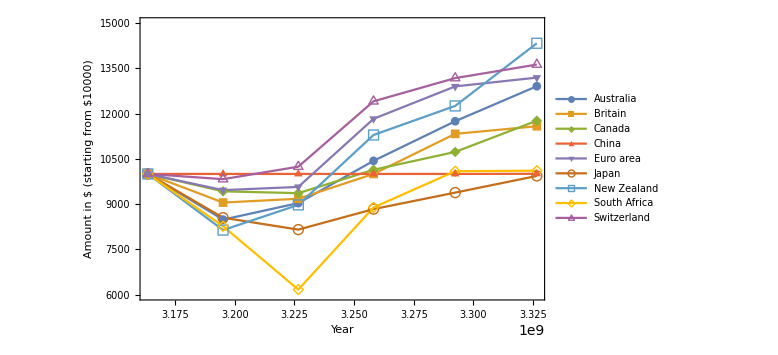

$10000 invested in 2000-2005.png

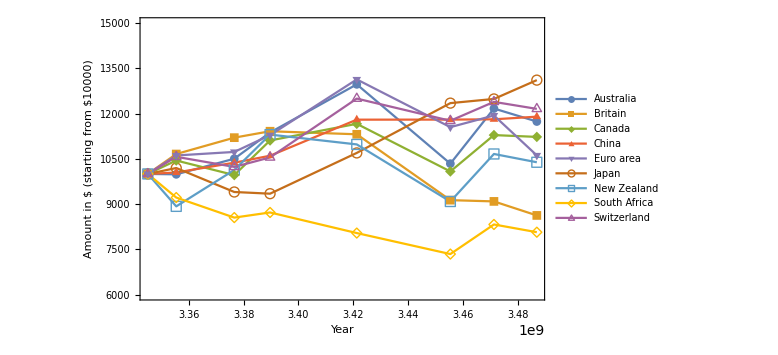

$10000 invested in 2005-2010.png

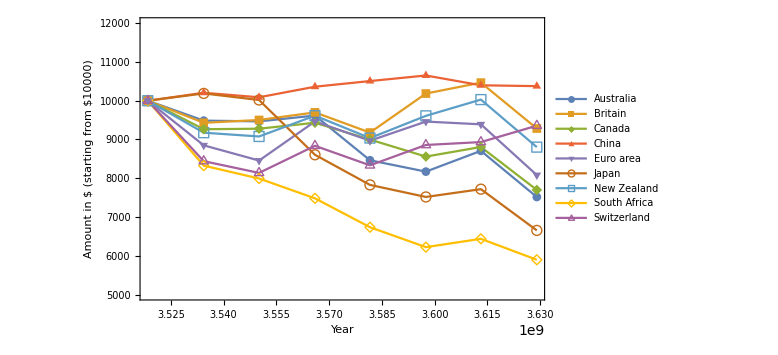

$10000 invested in 2010-2015.png

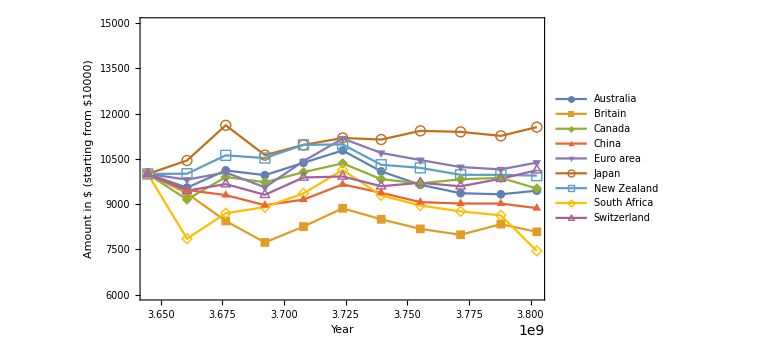

$10000 invested in 2015-2020.png

```mathematica
s=1;t=6;
plot3=DateListPlot[{info4[1,s,t],info4[2,s,t],info4[3,s,t],info4[4,s,t],info4[5,s,t],info4[6,s,t],info4[7,s,t],info4[8,s,t],info4[9,s,t]},PlotStyle->Thick,Frame->True,FrameStyle->Directive[Black,20],PlotMarkers->Automatic,ImageSize->Large,FrameLabel->{"Year","Amount in $ (starting from $10000)"},PlotLegends->{"Australia","Britain","Canada","China","Euro area","Japan","New Zealand","South Africa","Switzerland"},PlotRange->{6000,15000}]
Export["$10000 invested in 2000-2005.png",plot3]


s=7;t=14;
plot3=DateListPlot[{info4[1,s,t],info4[2,s,t],info4[3,s,t],info4[4,s,t],info4[5,s,t],info4[6,s,t],info4[7,s,t],info4[8,s,t],info4[9,s,t]},PlotStyle->Thick,Frame->True,FrameStyle->Directive[Black,20],PlotMarkers->Automatic,ImageSize->Large,FrameLabel->{"Year","Amount in $ (starting from $10000)"},PlotLegends->{"Australia","Britain","Canada","China","Euro area","Japan","New Zealand","South Africa","Switzerland"},PlotRange->{6000,15000}]
Export["$10000 invested in 2005-2010.png",plot3]



s=15;t=22;
plot3=DateListPlot[{info4[1,s,t],info4[2,s,t],info4[3,s,t],info4[4,s,t],info4[5,s,t],info4[6,s,t],info4[7,s,t],info4[8,s,t],info4[9,s,t]},PlotStyle->Thick,Frame->True,FrameStyle->Directive[Black,20],PlotMarkers->Automatic,ImageSize->Large,FrameLabel->{"Year","Amount in $ (starting from $10000)"},PlotLegends->{"Australia","Britain","Canada","China","Euro area","Japan","New Zealand","South Africa","Switzerland"},PlotRange->{5000,12000}]
Export["$10000 invested in 2010-2015.png",plot3]


s=23;t=33;
plot3=DateListPlot[{info4[1,s,t],info4[2,s,t],info4[3,s,t],info4[4,s,t],info4[5,s,t],info4[6,s,t],info4[7,s,t],info4[8,s,t],info4[9,s,t]},PlotStyle->Thick,Frame->True,FrameStyle->Directive[Black,20],PlotMarkers->Automatic,ImageSize->Large,FrameLabel->{"Year","Amount in $ (starting from $10000)"},PlotLegends->{"Australia","Britain","Canada","China","Euro area","Japan","New Zealand","South Africa","Switzerland"},PlotRange->{6000,15000}]
Export["$10000 invested in 2015-2020.png",plot3]
```

```mathematica
(* Calculate the most overvalued currency and the most undevalued currency for each year *)
ini=data[[1]][[2]];
maxlist=Array[f,33];
minlist=Array[f,33];
For[j=1,j≤33,j=j+1,
ini=data[[j]][[2]];
mini=data[[j]][[2]];
c=1;
s1=1;s11=1;s2=1;s21=1;
For[i=j+33,i≤Length[data],i=i+33,
c=c+1;
If[data[[i]][[2]]>ini,ini=data[[i]][[2]];s1=c;s11=i;
];
If[data[[i]][[2]]<mini,mini=data[[i]][[2]];s2=c;s21=i;
];
];
maxlist[[j]]={s1,s11,ini};
minlist[[j]]={s2,s21,mini};
]
```

```mathematica
strat2=Array[f1,{33,2}];q=1;
For[ii=1,ii≤Length[minlist],ii++,
p=minlist[[ii]][[1]];
If[ii>1,q=minlist[[ii-1]][[1]]];

strat2[[ii]][[1]]=info3[p][[ii]][[1]];
If[ii>1,
strat2[[ii]][[1]]=info3[p][[ii]][[1]];
strat2[[ii]][[2]]=strat2[[ii-1]][[2]]*info3[q][[ii-1]][[2]]/(info3[q][[ii]][[2]]),
strat2[[ii]][[2]]=10000]];
```

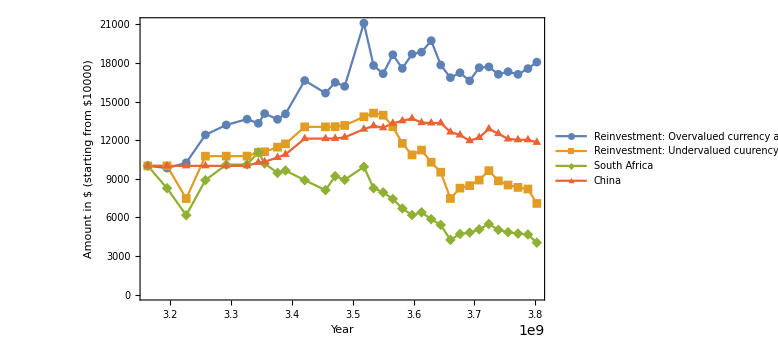

```mathematica
plot2=DateListPlot[{info2[9],strat2,info2[8],info2[4]},PlotStyle->Thick,Frame->True,FrameStyle->Directive[Black,20],PlotMarkers->Automatic,ImageSize->Large,FrameLabel->{"Year","Amount in $ (starting from $10000)"},PlotLegends->{"Reinvestment: Overvalued currency annually","Reinvestment: Undervalued cuurency annually","South Africa","China"}]
```

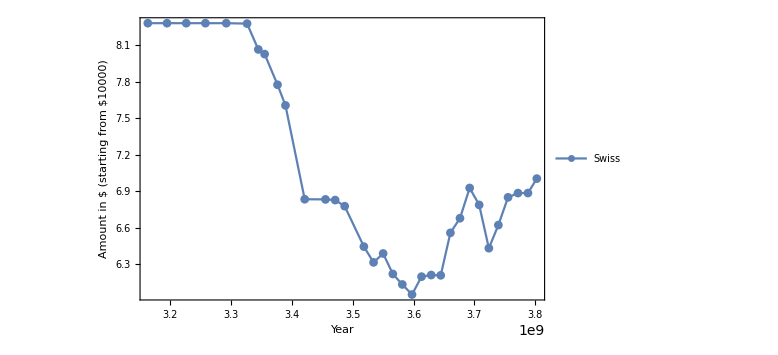
```mathematica
plot3=DateListPlot[{info3[1],info3[2],info3[3],info3[4],info3[5],info3[6],info3[7],info3[8],info3[9],info3[10]},PlotStyle->Thick,Frame->True,FrameStyle->Directive[Black,20],PlotMarkers->Automatic,ImageSize->Large,FrameLabel->{"Year","Amount in $ (starting from $10000)"},PlotLegends->{"Australia","Britain","Canada","China","Euro area","Japan","New Zealand","South Africa","Switzerland","USD"}];

-Graphics-
```

```mathematica
(****************************************************************************************************************)
(****************************************************************************************************************)
(****************************************************************************************************************)
(****************************************************************************************************************)
```

```mathematica
SetDirectory[NotebookDirectory[]];
f[x_]:=0
data=Array[f,5]
data[[1]]=Import["big-mac-2020-07-01.xls",{"Sheets","Jul2017"}][[2;;,{1,4,5,6,7,10,1,1,1,1,1,1,1}]];
data[[2]]=Import["big-mac-2020-07-01.xls",{"Sheets","Jul2016"}][[2;;,{1,4,5,6,7,10,1,1,1,1,1,1,1}]];
data[[3]]=Import["big-mac-2020-07-01.xls",{"Sheets","Jul2015"}][[2;;,{1,4,5,6,7,10,1,1,1,1,1,1,1}]];
data[[4]]=Import["big-mac-2020-07-01.xls",{"Sheets","Jul2014"}][[2;;,{1,4,5,6,7,10,1,1,1,1,1,1,1}]];
```

{0,0,0,0,0}

```mathematica
data[[1]]
```

```mathematica
data;
```

```mathematica
For[i=1,i≤Length[data],i++,
For[j=1,j≤Length[data[[i]]],j++,
data[[i]][[j]][[6]]=-(data[[i]][[j]][[3]]-data[[i]][[j]][[5]])/(data[[i]][[j]][[5]])*100;
data[[i]][[j]][[7]]=j
]]
```

```mathematica
data[[1]][[1]]
```

{UAE,14.,3.673,3.8116,2.64151,-39.0493,1,UAE,UAE,UAE,UAE,UAE,UAE}

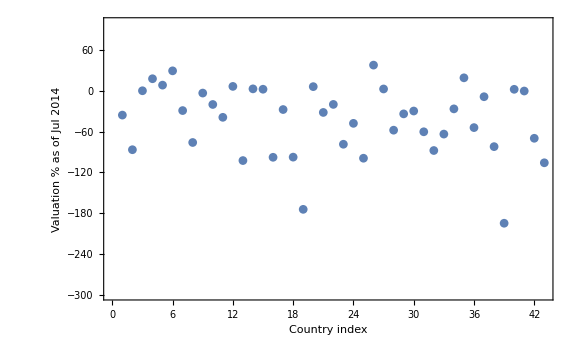

```mathematica
ListPlot[data[[4]][[1;;,{7,6}]],PlotRange->{-300,100},PlotStyle->Thick,Frame->True,FrameStyle->Directive[Black,20],PlotMarkers->Automatic,ImageSize->Large,FrameLabel->{"Country index","Valuation % as of Jul 2014"}]
```

```mathematica
For[i=1,i≤Length[data[[4]]],i++,
data[[4]][[i]][[9]]=10000;
data[[4]][[i]][[10]]=10000*(1+(data[[4]][[i]][[3]]-data[[3]][[i]][[3]])/data[[3]][[i]][[3]]);
data[[4]][[i]][[11]]=10000*(1+(data[[4]][[i]][[3]]-data[[2]][[i]][[3]])/data[[2]][[i]][[3]]);
data[[4]][[i]][[12]]=10000*(1+(data[[4]][[i]][[3]]-data[[1]][[i]][[3]])/data[[1]][[i]][[3]]);
]
```

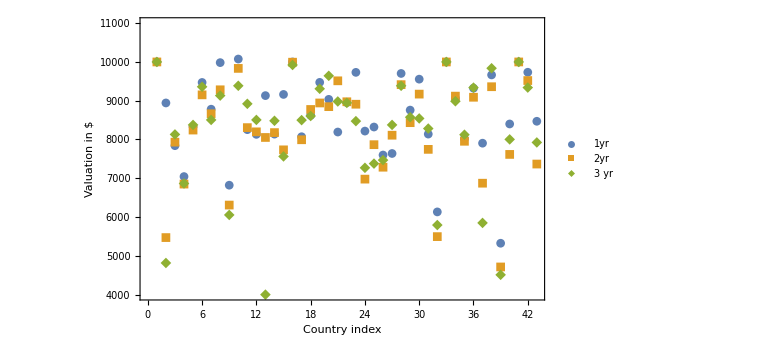

```mathematica
ListPlot[{data[[4]][[1;;,{7,10}]],data[[4]][[1;;,{7,11}]],data[[4]][[1;;,{7,12}]]},PlotLegends->{"1yr","2yr","3 yr"},Joined->False,PlotRange->{4000,11000},PlotStyle->Thick,Frame->True,FrameStyle->Directive[Black,20],PlotMarkers->Automatic,ImageSize->Large,FrameLabel->{"Country index","Valuation in $"}]
```